```mathematica
(*ClearAll[toDirective,styleJoin]
toDirective[{ps__}|ps__]:=Flatten[Directive@@Flatten[{#}]]&/@{ps}
styleJoin[style_,base_]:=Module[{ps,n},ps=toDirective/@{PlotStyle/.Options[base],style};
ps=ps/.Automatic:>Sequence[];
n=LCM@@Length/@ps;
MapThread[Join,PadRight[#,n,#]&/@ps]]
pp={Plot,ListPlot};
Unprotect/@pp;

(#[a__,b:OptionsPattern[]]:=Block[{$alsoPS=True,sh},sh=Cases[{b},("MessagesHead"->hd_):>hd,{-2},1]/.{{z_}:>z,{}->#};
With[{new=styleJoin[OptionValue[PlotStyle],sh]},#[a,PlotStyle->new,b]]]/;!TrueQ[$alsoPS])&/@pp;
SetOptions[pp,PlotStyle->Thickness[0.01]];
defThick=Thickness[0.005];*)
SetDirectory[NotebookDirectory[]];
SetOptions[Plot,BaseStyle-> {FontSize-> 12,Thick}];
SetOptions[LogPlot,BaseStyle-> {FontSize-> 12,Thick}];
SetOptions[LogLinearPlot,
BaseStyle-> {FontSize-> 12,Thick}];
SetOptions[LogLogPlot,BaseStyle-> {FontSize-> 12,Thick}];
```

```mathematica
Import["Figures-sources/entr_rhoratios/entropy_100MeV_0.5s_th2mu_10p_upd2_x.dat","Elements"];
(*Suffix Test corresponds to our results, Digit - are digitized results of others*)
```

InterpolatingFunction::dmval: Input value {0.0500047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

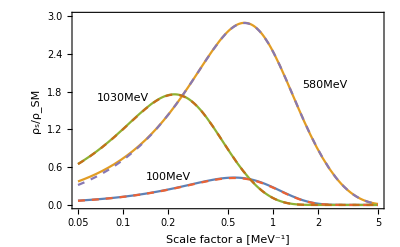

```mathematica
(*entr_rhoratios.eps*)
Entr100Test=Import["Figures-sources/entr_rhoratios/entropy_100MeV_0.5s_th2mu_10p_upd2_x.dat","HeaderLines"->2];
Entr580Test=Import["Figures-sources/entr_rhoratios/entropy_580MeV_1.01s_th2e_10p_upd2_x.dat","HeaderLines"->2];
Entr1030Test=Import["Figures-sources/entr_rhoratios/entropy_1030MeV_0.102s_th2tau_10p_upd2_x.dat","HeaderLines"->2];
Entr100Digit=Import["Figures-sources/entr_rhoratios/ratioRho100.dat","HeaderLines"->2];
Entr580Digit=Import["Figures-sources/entr_rhoratios/ratioRho580.dat","HeaderLines"->2];
Entr1030Digit=Import["Figures-sources/entr_rhoratios/ratioRho1030.dat","HeaderLines"->2];

Entr100TestListX=Entr100Test[[All,1]];
Entr100TestListY=Entr100Test[[All,30]]/(Entr100Test[[All,5]]+Entr100Test[[All,7]]+3*Entr100Test[[All,9]]);
Entr100TestFunc=Interpolation[Table[Insert[{Entr100TestListX[[i]]},Entr100TestListY[[i]],2],{i,Length[Entr100TestListX]}]];
Entr580TestListX=Entr580Test[[All,1]];
Entr580TestListY=Entr580Test[[All,30]]/(Entr580Test[[All,5]]+Entr580Test[[All,7]]+3*Entr580Test[[All,9]]);
Entr580TestFunc=Interpolation[Table[Insert[{Entr580TestListX[[i]]},Entr580TestListY[[i]],2],{i,Length[Entr580TestListX]}]];
Entr1030TestListX=Entr1030Test[[All,1]];
Entr1030TestListY=Entr1030Test[[All,30]]/(Entr1030Test[[All,5]]+Entr1030Test[[All,7]]+3*Entr1030Test[[All,9]]);
Entr1030TestFunc=Interpolation[Table[Insert[{Entr1030TestListX[[i]]},Entr1030TestListY[[i]],2],{i,Length[Entr1030TestListX]}]];
Entr100DigitFunc=Interpolation[Entr100Digit[[All,{2,3}]]];
Entr580DigitFunc=Interpolation[Entr580Digit[[All,{2,3}]]];
Entr1030DigitFunc=Interpolation[Entr1030Digit[[All,{2,3}]]];

LogLinearPlot[{Entr100TestFunc[x],Entr580TestFunc[x],Entr1030TestFunc[x],Entr100DigitFunc[x],Entr580DigitFunc[x],Entr1030DigitFunc[x]},{x,0.05,5},PlotRange->{{0.05,5},{0,3}},Frame->True,FrameLabel->{"Scale factor a [MeV^-1]","ρ_s/ρ_SM"},PlotStyle->{{},{},{},{Dashed},{Dashed},{Dashed}},Epilog->{Text["1030MeV",{Log[0.1],1.7}],Text["580MeV",{Log[2.2],1.9}],Text["100MeV",{Log[0.2],.45}]}]
Export["Figures-sources/entr_rhoratios.eps",%];
```

InterpolatingFunction::dmval: Input value {0.100009} lies outside the range of data in the interpolating function. Extrapolation will be used.

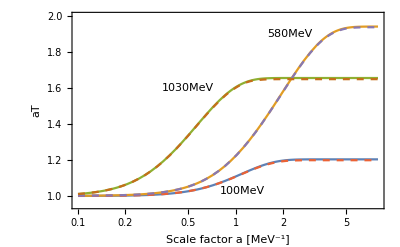

```mathematica
(*ent_Tx.eps*)
Entr100Test=Import["Figures-sources/ent_Tx/entropy_100MeV_0.5s_th2mu_10p_upd2_x.dat","HeaderLines"->2];
Entr580Test=Import["Figures-sources/ent_Tx/entropy_580MeV_1.01s_th2e_10p_upd2_x.dat","HeaderLines"->2];
Entr1030Test=Import["Figures-sources/ent_Tx/entropy_1030MeV_0.102s_th2tau_10p_upd2_x.dat","HeaderLines"->2];
Entr100Digit=Import["Figures-sources/ent_Tx/Tx100.dat","HeaderLines"->2];
Entr580Digit=Import["Figures-sources/ent_Tx/Tx580.dat","HeaderLines"->2];
Entr1030Digit=Import["Figures-sources/ent_Tx/Tx1030.dat","HeaderLines"->2];

Entr100TestFunc=Interpolation[Entr100Test[[All,{1,3}]]];
Entr580TestFunc=Interpolation[Entr580Test[[All,{1,3}]]];
Entr1030TestFunc=Interpolation[Entr1030Test[[All,{1,3}]]];
Entr100DigitFunc=Interpolation[Entr100Digit[[All,{2,3}]]];
Entr580DigitFunc=Interpolation[Entr580Digit[[All,{2,3}]]];
Entr1030DigitFunc=Interpolation[Entr1030Digit[[All,{2,3}]]];

LogLinearPlot[{Entr100TestFunc[x],Entr580TestFunc[x],Entr1030TestFunc[x],Entr100DigitFunc[x],Entr580DigitFunc[x],Entr1030DigitFunc[x]},{x,0.1,8},PlotRange->{{0.1,8},{0.95,2}},Frame->True,FrameLabel->{"Scale factor a [MeV^-1]","aT"},PlotStyle->{{},{},{},{Dashed},{Dashed},{Dashed}},Epilog->{Text["1030MeV",{Log[0.5],1.6}],Text["580MeV",{Log[2.2],1.9}],Text["100MeV",{Log[1.1],1.03}]}]
Export["Figures-sources/ent_Tx.eps",%];
```

InterpolatingFunction::dmval: Input value {0.0500054} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

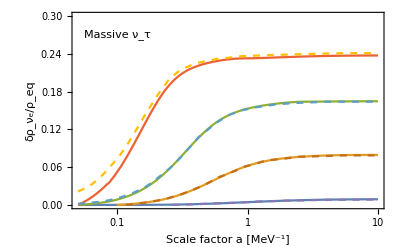

```mathematica
(*masstau_drhonue_comp.eps*)
DrhoSMTest=Import["Figures-sources/masstau_drhonue_comp/semi_sm_upd_x.dat","HeaderLines"->2];
Drho3Test=Import["Figures-sources/masstau_drhonue_comp/masstau_3mev_upd_x.dat","HeaderLines"->2];
Drho7Test=Import["Figures-sources/masstau_drhonue_comp/masstau_7mev_upd_x.dat","HeaderLines"->2];
Drho20Test=Import["Figures-sources/masstau_drhonue_comp/masstau_20mev_upd2_x.dat","HeaderLines"->2];
DrhoSMDigit=Import["Figures-sources/masstau_drhonue_comp/drho0_1_imp.dat","HeaderLines"->1];
Drho3Digit=Import["Figures-sources/masstau_drhonue_comp/drho3_1_imp.dat","HeaderLines"->1];
Drho7Digit=Import["Figures-sources/masstau_drhonue_comp/drho7_1_imp.dat","HeaderLines"->1];
Drho20Digit=Import["Figures-sources/masstau_drhonue_comp/drho20_1_imp.dat","HeaderLines"->1];


DrhoSMTestFunc=Interpolation[DrhoSMTest[[All,{1,9}]]];
Drho3TestFunc=Interpolation[Drho3Test[[All,{1,9}]]];
Drho7TestFunc=Interpolation[Drho7Test[[All,{1,9}]]];
Drho20TestFunc=Interpolation[Drho20Test[[All,{1,9}]]];

DrhoSMDigitFunc=Interpolation[DrhoSMDigit[[All,{1,2}]],InterpolationOrder->1];
Drho3DigitFunc=Interpolation[Drho3Digit[[All,{1,2}]],InterpolationOrder->1];
Drho7DigitFunc=Interpolation[Drho7Digit[[All,{1,2}]],InterpolationOrder->1];
Drho20DigitFunc=Interpolation[Drho20Digit[[All,{1,2}]],InterpolationOrder->1];

(*Numerical constant from the .gp source*)
K=1./0.575727;
LogLinearPlot[{DrhoSMTestFunc[x]*K-1,Drho3TestFunc[x]*K-1,Drho7TestFunc[x]*K-1,Drho20TestFunc[x]*K-1,DrhoSMDigitFunc[x],Drho3DigitFunc[x],Drho7DigitFunc[x],Drho20DigitFunc[x]},{x,0.05,10},PlotRange->{{0.05,10},{0.,0.3}},Frame->True,FrameLabel->{"Scale factor a [MeV^-1]","δρ_ν_e/ρ_eq"},PlotStyle->{{},{},{},{},{Dashed},{Dashed},{Dashed},{Dashed}},Epilog->{Text["Massive ν_τ",{Log[0.1],0.27}]}]
Export["Figures-sources/masstau_drhonue_comp.eps",%];
```

InterpolatingFunction::dmval: Input value {0.0502033} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

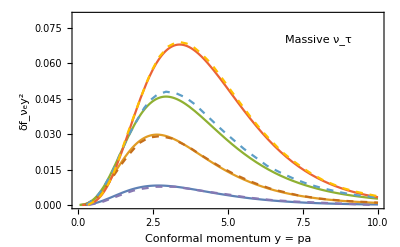

```mathematica
(*masstau_fnue_comp.eps*)
Df1Test=Import["Figures-sources/masstau_fnue_comp/masstau_1mev_upd.dat","HeaderLines"->2];
Df3Test=Import["Figures-sources/masstau_fnue_comp/masstau_3mev_upd.dat","HeaderLines"->2];
Df7Test=Import["Figures-sources/masstau_fnue_comp/masstau_7mev_upd.dat","HeaderLines"->2];
Df20Test=Import["Figures-sources/masstau_fnue_comp/masstau_20mev_upd.dat","HeaderLines"->2];
Df1Digit=Import["Figures-sources/masstau_fnue_comp/df_1_imp.dat","HeaderLines"->1];
Df3Digit=Import["Figures-sources/masstau_fnue_comp/df_3_imp.dat","HeaderLines"->1];
Df7Digit=Import["Figures-sources/masstau_fnue_comp/df_7_imp.dat","HeaderLines"->1];
Df20Digit=Import["Figures-sources/masstau_fnue_comp/df_20_imp.dat","HeaderLines"->1];
(*Fermi function*)
nF[z_]:=1/(Exp[z]+1);

Df1TestListX=Df1Test[[All,1]];
Df1TestListY=(Df1Test[[All,4]]-nF[Df1TestListX])*Df1TestListX^2;
Df1TestFunc=Interpolation[Table[Insert[{Df1TestListX[[i]]},Df1TestListY[[i]],2],{i,Length[Df1TestListX]}]];
Df3TestListX=Df3Test[[All,1]];
Df3TestListY=(Df3Test[[All,4]]-nF[Df3TestListX])*Df3TestListX^2;
Df3TestFunc=Interpolation[Table[Insert[{Df3TestListX[[i]]},Df3TestListY[[i]],2],{i,Length[Df3TestListX]}]];
Df7TestListX=Df7Test[[All,1]];
Df7TestListY=(Df7Test[[All,4]]-nF[Df7TestListX])*Df7TestListX^2;
Df7TestFunc=Interpolation[Table[Insert[{Df7TestListX[[i]]},Df7TestListY[[i]],2],{i,Length[Df7TestListX]}]];
Df20TestListX=Df20Test[[All,1]];
Df20TestListY=(Df20Test[[All,4]]-nF[Df20TestListX])*Df20TestListX^2;
Df20TestFunc=Interpolation[Table[Insert[{Df20TestListX[[i]]},Df20TestListY[[i]],2],{i,Length[Df20TestListX]}]];

Df1DigitFunc=Interpolation[Df1Digit[[All,{1,2}]],InterpolationOrder->1];
Df3DigitFunc=Interpolation[Df3Digit[[All,{1,2}]],InterpolationOrder->1];
Df7DigitFunc=Interpolation[Df7Digit[[All,{1,2}]],InterpolationOrder->1];
Df20DigitFunc=Interpolation[Df20Digit[[All,{1,2}]],InterpolationOrder->1];

Plot[{Df1TestFunc[x],Df3TestFunc[x],Df7TestFunc[x],Df20TestFunc[x],Df1DigitFunc[x],Df3DigitFunc[x],Df7DigitFunc[x],Df20DigitFunc[x]},{x,0.05,10},PlotRange->{{0.,10.},{0.,0.08}},Frame->True,FrameLabel->{"Conformal momentum y = pa","δf_ν_ey^2"},PlotStyle->{{},{},{},{},{Dashed},{Dashed},{Dashed},{Dashed}},Epilog->{Text["Massive ν_τ",{8,0.07}]}]
Export["Figures-sources/masstau_fnue_comp.eps",%];
```

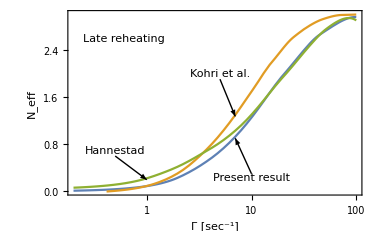

```mathematica
(*Neff_Gamma_comp.eps*)
KKSTest=Import["Figures-sources/Neff-Gamma_comp/kks4_summary.dat","HeaderLines"->1];
KKSDigit=Import["Figures-sources/Neff-Gamma_comp/kks_tau.dat","HeaderLines"->1];
HanneDigit=Import["Figures-sources/Neff-Gamma_comp/hanne_g.dat","HeaderLines"->1];

KKSTestFunc=Interpolation[KKSTest[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
KKSDigitFunc=Interpolation[KKSDigit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
HanneDigitFunc=Interpolation[HanneDigit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];

LogLinearPlot[{KKSTestFunc[x],KKSDigitFunc[x],HanneDigitFunc[x]},{x,0.2,100},PlotRange->{{0.2,100},{0.,3}},Frame->True,FrameLabel->{"Γ [sec^-1]","N_eff"},PlotStyle->{},Epilog->{Text["Late reheating",{Log[0.6],2.6}],Text["Present result",{Log[10],0.25}],Text["Hannestad",{Log[0.5],0.7}],Text["Kohri et al.",{Log[5],2.}],Arrow[{{Log[10],0.3},{Log[7],0.9}}],Arrow[{{Log[0.5],0.6},{Log[1],0.2}}],Arrow[{{Log[5],1.9},{Log[7],1.27}}]}]
Export["Figures-sources/Neff_Gamma_comp.eps",%];
```

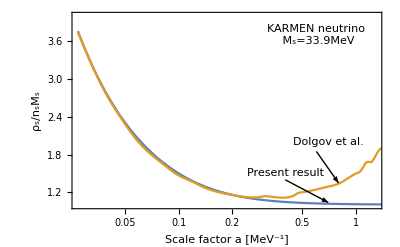

```mathematica
(*rhosns_comp03.eps*)
DolgovTest=Import["Figures-sources/rhosns_comp03/03sec_nudec12_x.dat","HeaderLines"->1];
DolgovDigit=Import["Figures-sources/rhosns_comp03/ratio_rhos_ns03_semikoz.dat"];
(*Mass of the KARMEN neutrino*)
MKarmen=33.9;
DolgovTestX=DolgovTest[[All,1]];
DolgovTestY=DolgovTest[[All,30]]/DolgovTest[[All,31]]/DolgovTestX/MKarmen;
DolgovTestFunc=Interpolation[Table[Insert[{DolgovTestX[[i]]},DolgovTestY[[i]],2],{i,Length[DolgovTestX]}]];

DolgovDigitFunc=Interpolation[DolgovDigit[[All,{1,2}]]];

LogLinearPlot[{DolgovTestFunc[x],DolgovDigitFunc[x]},{x,0.027,100},PlotRange->{{0.027,1.3},{1,4}},Frame->True,FrameLabel->{"Scale factor a [MeV^-1]","ρ_s/n_sM_s"},PlotStyle->{},Epilog->{Text["Dolgov et al.",{Log[0.7],2}],Text["Present result",{Log[0.4],1.5}],Text["KARMEN neutrino
 M_s=33.9MeV",{Log[0.6],3.7}],Arrow[{{Log[0.6],1.85},{Log[0.8],1.35}}],Arrow[{{Log[0.4],1.4},{Log[0.7],1.04}}]}]
Export["Figures-sources/rhosns_comp03.eps",%];
```

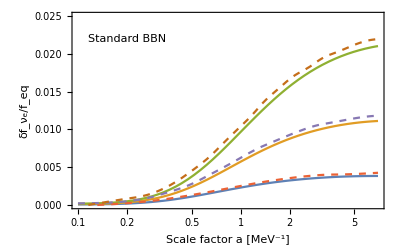

```mathematica
(*sm-deltafnue_comp.eps*)
deltafnueTest=Import["Figures-sources/sm-deltafnue_comp/semi_sm_upd_x.dat","HeaderLines"->2];
deltafnue3Digit=Import["Figures-sources/sm-deltafnue_comp/sm-dfnue3-semi.dat","HeaderLines"->1];
deltafnue5Digit=Import["Figures-sources/sm-deltafnue_comp/sm-dfnue5-semi.dat","HeaderLines"->1];
deltafnue7Digit=Import["Figures-sources/sm-deltafnue_comp/sm-dfnue7-semi.dat","HeaderLines"->1];

deltafnue3TestFunc=Interpolation[deltafnueTest[[All,{1,13}]]];
deltafnue5TestFunc=Interpolation[deltafnueTest[[All,{1,14}]]];
deltafnue7TestFunc=Interpolation[deltafnueTest[[All,{1,15}]]];
deltafnue3DigitFunc=Interpolation[deltafnue3Digit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
deltafnue5DigitFunc=Interpolation[deltafnue5Digit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
deltafnue7DigitFunc=Interpolation[deltafnue7Digit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];

LogLinearPlot[{deltafnue3TestFunc[x]*(Exp[3]+1)-1,deltafnue5TestFunc[x]*(Exp[5]+1)-1,deltafnue7TestFunc[x]*(Exp[7]+1)-1,deltafnue3DigitFunc[x],deltafnue5DigitFunc[x],deltafnue7DigitFunc[x]},{x,0.1,7},PlotRange->{{0.1,7},{0,0.025}},Frame->True,FrameLabel->{"Scale factor a [MeV^-1]","δf_ν_e/f_eq"},PlotStyle->{{},{},{},{Dashed},{Dashed},{Dashed}},Epilog->{Text["Standard BBN",{Log[0.2],0.022}]}]
Export["Figures-sources/sm-deltafnue_comp.eps",%];
```

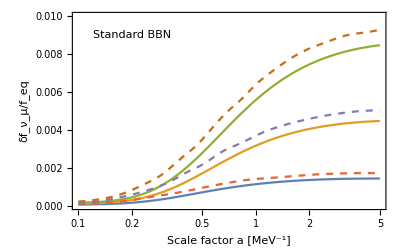

```mathematica
(*sm-deltafnumu_comp.eps*)
deltafnueTest=Import["Figures-sources/sm-deltafnumu_comp/semi_sm_upd_x.dat","HeaderLines"->2];
deltafnue3Digit=Import["Figures-sources/sm-deltafnumu_comp/sm-dfnumu3-semi.dat","HeaderLines"->1];
deltafnue5Digit=Import["Figures-sources/sm-deltafnumu_comp/sm-dfnumu5-semi.dat","HeaderLines"->1];
deltafnue7Digit=Import["Figures-sources/sm-deltafnumu_comp/sm-dfnumu7-semi.dat","HeaderLines"->1];

deltafnue3TestFunc=Interpolation[deltafnueTest[[All,{1,27}]]];
deltafnue5TestFunc=Interpolation[deltafnueTest[[All,{1,28}]]];
deltafnue7TestFunc=Interpolation[deltafnueTest[[All,{1,29}]]];
deltafnue3DigitFunc=Interpolation[deltafnue3Digit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
deltafnue5DigitFunc=Interpolation[deltafnue5Digit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
deltafnue7DigitFunc=Interpolation[deltafnue7Digit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];

LogLinearPlot[{deltafnue3TestFunc[x]*(Exp[3]+1)-1,deltafnue5TestFunc[x]*(Exp[5]+1)-1,deltafnue7TestFunc[x]*(Exp[7]+1)-1,deltafnue3DigitFunc[x],deltafnue5DigitFunc[x],deltafnue7DigitFunc[x]},{x,0.1,5},PlotRange->{{0.1,5},{0,0.01}},Frame->True,FrameLabel->{"Scale factor a [MeV^-1]","δf_ν_μ/f_eq"},PlotStyle->{{},{},{},{Dashed},{Dashed},{Dashed}},Epilog->{Text["Standard BBN",{Log[0.2],0.009}]}]
Export["Figures-sources/sm-deltafnumu_comp.eps",%];
```

Import::nffil: File not found during Import.

InterpolatingFunction::dmval: Input value {0.500045} lies outside the range of data in the interpolating function. Extrapolation will be used.

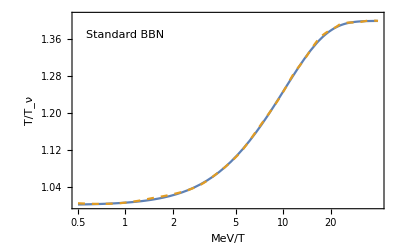

```mathematica
(*sm-Tx_comp.eps*)
smTx2015Test = Import["../tests/cosmic_neutrino_background/sm_temp_2015.dat", "HeaderLines"->1];
smTxTest=Import["Figures-sources/sm-Tx_comp/semi_sm_upd_x.dat","HeaderLines"->2];
smTxTestFunc=Interpolation[smTxTest[[All,{1,3}]]];
smTxDigit=Import["Figures-sources/sm-Tx_comp/sm_temp.dat","HeaderLines"->1];
smTxDigitFunc=Interpolation[smTxDigit[[All,{1,2}]]];

LogLinearPlot[{smTxTestFunc[x],smTxDigitFunc[x]},{x,0.5,40},PlotRange->{{0.5,40},{1,1.41}},Frame->True,FrameLabel->{"MeV/T","T/T_ν"},PlotStyle->{{},{Dashed}},Epilog->{Text["Standard BBN",{Log[1],1.37}]}]
Export["Figures-sources/sm-Tx_comp.eps",%];
```

InterpolatingFunction::dmval: Input value {0.000224714} lies outside the range of data in the interpolating function. Extrapolation will be used.

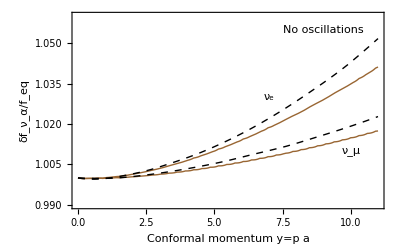

```mathematica
(*final-spectra-SM.eps*)
finalspectraSMTest=Import["Figures-sources/Final-spectra-SM/spectra-test-SM.dat","HeaderLines"->3];
finalspectranueSMDigit=Import["Figures-sources/Final-spectra-SM/Mangano-nue-noosc.tsv"];
finalspectranumuSMDigit=Import["Figures-sources/Final-spectra-SM/Mangano-numu-noosc.tsv"];
finalnueSMTestFunc=Interpolation[finalspectraSMTest[[All,{1,4}]]];
finalnumuSMTestFunc=Interpolation[finalspectraSMTest[[All,{1,8}]]];
finalspectranueSMDigitFunc=Interpolation[finalspectranueSMDigit[[All,{1,2}]]];
finalspectranumuSMDigitFunc=Interpolation[finalspectranumuSMDigit[[All,{1,2}]]];

Plot[{finalnueSMTestFunc[y]*(Exp[y]+1),finalnumuSMTestFunc[y]*(Exp[y]+1),finalspectranueSMDigitFunc[y],finalspectranumuSMDigitFunc[y]},{y,0,11},PlotRange->{{0,11},{0.99,1.06}},Frame->True,FrameLabel->{"Conformal momentum y=p a","δf_ν_α/f_eq"},PlotStyle->{{Brown},{Brown},{Black,Dashed},{Black,Dashed}},Epilog->{Text["ν_e",{7,1.03}],Text["ν_μ",{10,1.01}],Text["No oscillations",{9,1.055}]}]
Export["Figures-sources/final-spectra-SM-noosc.eps",%];
```

InterpolatingFunction::dmval: Input value {0.000224714} lies outside the range of data in the interpolating function. Extrapolation will be used.

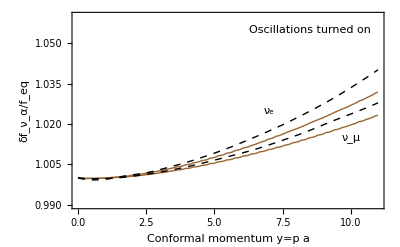

```mathematica
finalspectraSMth13zeroTest=Import["Figures-sources/Final-spectra-SM/oscillations+SM-th13=0.dat","HeaderLines"->3];
finalspectranueSMDigit=Import["Figures-sources/Final-spectra-SM/Mangano-nue-th13=0.tsv"];
finalspectranumuSMDigit=Import["Figures-sources/Final-spectra-SM/Mangano-numu-th13=0.tsv"];
finalnueSMth13zeroTestFunc=Interpolation[finalspectraSMth13zeroTest[[All,{1,4}]]];
finalnumuSMth13zeroTestFunc=Interpolation[finalspectraSMth13zeroTest[[All,{1,8}]]];
finalnutauSMth13zeroTestFunc=Interpolation[finalspectraSMth13zeroTest[[All,{1,12}]]];
finalspectranueSMth13zeroDigitFunc=Interpolation[finalspectranueSMDigit[[All,{1,2}]]];
finalspectranumuSMth13zeroDigitFunc=Interpolation[finalspectranumuSMDigit[[All,{1,2}]]];
"To get from the basis of nu_mu and nu_tau we used (with theta_23=0) to the physical basis, used by Mangano, we take an average of the distributions";
Plot[{finalnueSMth13zeroTestFunc[y]*(Exp[y]+1),0.5(finalnumuSMth13zeroTestFunc[y]+finalnutauSMth13zeroTestFunc[y])*(Exp[y]+1),finalspectranueSMth13zeroDigitFunc[y],finalspectranumuSMth13zeroDigitFunc[y]},{y,0,11},PlotRange->{{0,11},{0.99,1.06}},Frame->True,FrameLabel->{"Conformal momentum y=p a","δf_ν_α/f_eq"},PlotStyle->{{Brown},{Brown},{Black,Dashed},{Black,Dashed}},Epilog->{Text["ν_e",{7,1.025}],Text["ν_μ",{10,1.015}],Text["Oscillations turned on",{8.5,1.055}]}]
Export["Figures-sources/final-spectra-SM-osc-th13=0.eps",%];
```